# Prime Difference Sequences and Cellular Automata

Exploring possible interfaces between primes (analytic number theory) and the space of CA rulesets

## What does it look like when we visualize the spacing between consecutive Prime Numbers?

When looking at prime numbers, one of the distinctive patterns is the spacing between consecutive primes. In order to do this, we can write a function which takes the differences between n consecutive primes in a nested list corresponding to a finite difference table of absolute differences:

```mathematica
PrimeDifferences[n_]:=NestList[Abs[Differences[#]]&,Table[Prime[i],{i,1,n}],n-1]
```

Now we can look at one of these nested lists for the first 25 primes. Just looking at the raw data, we see that after a certain number of steps, all the data turns to being only 2s and 0s except for a constant 1 at the start of each list step:

```mathematica
example1=PrimeDifferences[25]
```

{{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97},{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8},{1,0,2,2,2,2,2,2,4,4,2,2,2,2,0,4,4,2,2,4,2,2,2},{1,2,0,0,0,0,0,2,0,2,0,0,0,2,4,0,2,0,2,2,0,0},{1,2,0,0,0,0,2,2,2,2,0,0,2,2,4,2,2,2,0,2,0},{1,2,0,0,0,2,0,0,0,2,0,2,0,2,2,0,0,2,2,2},{1,2,0,0,2,2,0,0,2,2,2,2,2,0,2,0,2,0,0},{1,2,0,2,0,2,0,2,0,0,0,0,2,2,2,2,2,0},{1,2,2,2,2,2,2,2,0,0,0,2,0,0,0,0,2},{1,0,0,0,0,0,0,2,0,0,2,2,0,0,0,2},{1,0,0,0,0,0,2,2,0,2,0,2,0,0,2},{1,0,0,0,0,2,0,2,2,2,2,2,0,2},{1,0,0,0,2,2,2,0,0,0,0,2,2},{1,0,0,2,0,0,2,0,0,0,2,0},{1,0,2,2,0,2,2,0,0,2,2},{1,2,0,2,2,0,2,0,2,0},{1,2,2,0,2,2,2,2,2},{1,0,2,2,0,0,0,0},{1,2,0,2,0,0,0},{1,2,2,2,0,0},{1,0,0,2,0},{1,0,2,2},{1,2,0},{1,2},{1}}

When we create an array plot of the first 200 primes and their difference steps data where each of the zeros is turned to black and each other number (mostly 2s) becomes gray, we see an image that looks very much like a cellular automaton. The black triangles are clusters of zeros in the difference table corresponding to our array plot:

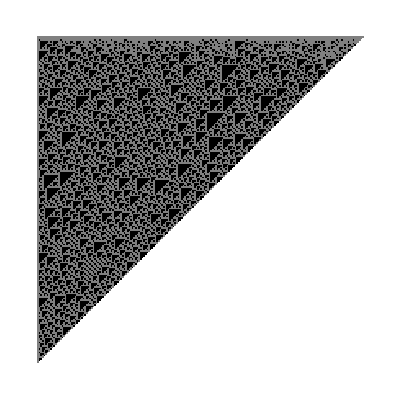

This pattern is a modern visualization of something recorded as discovered and published by François Proth in 1878 and Norman L. Gilbreath in 1958. It is usually called Gilbreath’s conjecture, where the first entries in each step are conjectured to follow the series 2,1,1,1,1,1,1,1.....

## Is this patterning an artifact particular to spacing in prime fields?

In order to test whether this patterning is particular to the field of primes, we can compare it with random data generating array plots corresponding to absolute difference tables.

```mathematica
RandomDifferences[n_,k_]:=NestList[Abs[Differences[#]]&,RandomInteger[{1,k},n],n-1]
```

First an example with 25 integers all below an upper bound of 6:

```mathematica
example2=RandomDifferences[25,6]
```

{{4,1,5,6,5,5,2,3,5,5,4,5,6,1,5,4,4,4,3,4,6,4,3,2,4},{3,4,1,1,0,3,1,2,0,1,1,1,5,4,1,0,0,1,1,2,2,1,1,2},{1,3,0,1,3,2,1,2,1,0,0,4,1,3,1,0,1,0,1,0,1,0,1},{2,3,1,2,1,1,1,1,1,0,4,3,2,2,1,1,1,1,1,1,1,1},{1,2,1,1,0,0,0,0,1,4,1,1,0,1,0,0,0,0,0,0,0},{1,1,0,1,0,0,0,1,3,3,0,1,1,1,0,0,0,0,0,0},{0,1,1,1,0,0,1,2,0,3,1,0,0,1,0,0,0,0,0},{1,0,0,1,0,1,1,2,3,2,1,0,1,1,0,0,0,0},{1,0,1,1,1,0,1,1,1,1,1,1,0,1,0,0,0},{1,1,0,0,1,1,0,0,0,0,0,1,1,1,0,0},{0,1,0,1,0,1,0,0,0,0,1,0,0,1,0},{1,1,1,1,1,1,0,0,0,1,1,0,1,1},{0,0,0,0,0,1,0,0,1,0,1,1,0},{0,0,0,0,1,1,0,1,1,1,0,1},{0,0,0,1,0,1,1,0,0,1,1},{0,0,1,1,1,0,1,0,1,0},{0,1,0,0,1,1,1,1,1},{1,1,0,1,0,0,0,0},{0,1,1,1,0,0,0},{1,0,0,1,0,0},{1,0,1,1,0},{1,1,0,1},{0,1,1},{1,0},{1}}

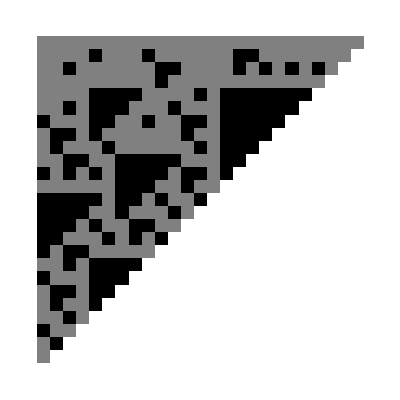

```mathematica
ArrayPlot[example2/.{0->2,a_Integer/;a>0->1}]
```

And now an example with 200 random integers all below an upper bound of 57:

```mathematica
example3=RandomDifferences[200,57];
```

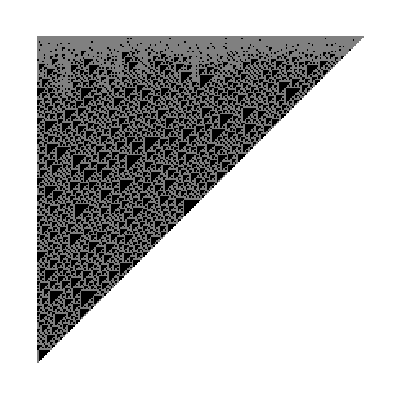

```mathematica
ArrayPlot[example3/.{0->2,a_Integer/;a>0->1}]
```

We see in both examples that to the human eye they appear to look similar with “random” triangles of various size and placement (corresponding to clusters of 0s) in a way similar to the prime field array plot.

We also see by looking at the raw data that at some point in each example the difference steps becomes purely binary (this time all 1s and 0s rather than mostly 2s and 0s).

## Is there a CA ruleset that corresponds to the spacing between consecutive Prime Numbers?

By looking at the first difference step where the data becomes 2s and 0s (except for first entry which is 1) from example 1 above, we can find exactly which CA ruleset from the 256 possible elementary cellular automata as described in NKS corresponds to the process of taking absolute values of differences.

The first step in example 1 to do this is step 6:

```mathematica
example1[[6]]
```

{1,2,0,0,0,2,0,0,0,2,0,2,0,2,2,0,0,2,2,2}

Now we are going to drop the first element from the list and turn all the 2s into 1s to give us a nice binary sequence

```mathematica
init=Rest[example1[[6]]]/2
```

{1,0,0,0,1,0,0,0,1,0,1,0,1,1,0,0,1,1,1}

```mathematica
DifferencesCA[init_]:=MapIndexed[Drop[#1,1-First[#2]]&,CellularAutomaton[102,init,Length[init]-1]]
```

```mathematica
example4=DifferencesCA[init]
```

{{1,0,0,0,1,0,0,0,1,0,1,0,1,1,0,0,1,1,1},{1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,1,0,0},{1,0,1,0,1,0,1,0,0,0,0,1,1,1,1,1,0},{1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,1},{0,0,0,0,0,1,1,0,1,0,1,0,0,1},{0,0,0,0,1,0,1,1,1,1,1,0,1},{0,0,0,1,1,1,0,0,0,0,1,1},{0,0,1,0,0,1,0,0,0,1,0},{0,1,1,0,1,1,0,0,1,1},{1,0,1,1,0,1,0,1,0},{1,1,0,1,1,1,1,1},{0,1,1,0,0,0,0},{1,0,1,0,0,0},{1,1,1,0,0},{0,0,1,0},{0,1,1},{1,0},{1}}

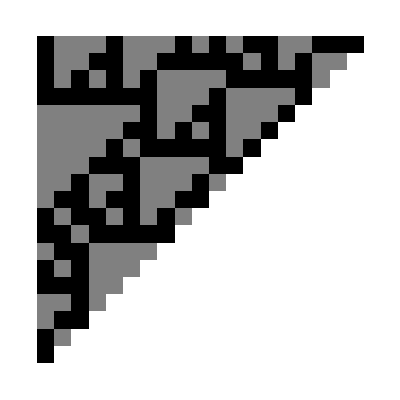

```mathematica
ArrayPlot[example4/.{0->1,1->2}]
```

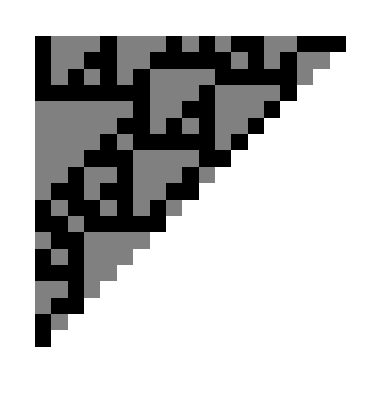

```mathematica
ArrayPlot[Rest/@Take[example1,{6,-1}]/. 0->1]
```

The two above array plots look EXACTLY THE SAME, but the first one was generated from elementary cellular automaton rule 102, while the second image was generated from step 6 of successive differences between consecutive primes with the first element removed. These two systems correspond.

Further Explorations

Could any further interfaces between CAs and prime numbers be discovered?

Authorship information

Daniel Reynolds

6/19-6/23/17

dreynoldsling@gmail.com